Definições Iniciais

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[ToFileName[Extract["FileName" /. NotebookInformation[EvaluationNotebook[]], {1}, FrontEnd`FileName]]]
```

/home/gbcaminha/repositorios/sltools/PerturbativeMethod/examples

(* Checking Alard 08 Fig 8 and eq. 17
MSSG; Sept 27, 2010
Output suppressed until plot by terminal semicolons *)

```mathematica
(* First deriv: df0/dtheta, see eq. 17 *)
```

```mathematica
dfdt[eta_,mp_, rp_,thetap_,theta_]=eta  Sin[2*theta] + mp rp Sin[theta-thetap] / Sqrt[1-2 rp Cos[theta-thetap] + rp^2];
```

```mathematica
(* Second deriv: d2f0/dtheta2 *)
```

```mathematica
df2dt[eta_,mp_, rp_,thetap_,theta_] = D[dfdt[eta,mp, rp,thetap,theta], theta];
```

```mathematica
(* Caustic x-position in source plane *)
```

```mathematica
cy1[eta_,mp_, rp_,thetap_,theta_] = df2dt[eta,mp, rp,thetap,theta] Cos[theta] + dfdt[eta,mp, rp,thetap,theta] Sin[theta];
```

```mathematica
(* Caustic y-position in source plane *)
```

```mathematica
cy2[eta_,mp_, rp_,thetap_,theta_] = df2dt[eta,mp, rp,thetap,theta] Sin[theta] - dfdt[eta,mp, rp,thetap,theta] Cos[theta];
```

```mathematica
(* Plot for only elliptical central potential -- red *)
```

```mathematica
p1 = ParametricPlot[{cy1[0.1, 0.0, 0, 0, t],cy2[0.1, 0.0, 0, 0, t]},{t,0,2*Pi}, PlotStyle->Red];
```

```mathematica
(* Plot with elliptical central potential and perturber at theta_p = 0 -- green *)
```

```mathematica
p2 = ParametricPlot[{cy1[0.1, 0.03, 1.3, 0, t],cy2[0.1, 0.03, 1.3, 0, t]},{t,0,2*Pi}, PlotStyle->Green];
```

```mathematica
(* Plot with elliptical central potential and perturber at theta_p = Pi/10 -- blue*)
```

```mathematica
p3 = ParametricPlot[{cy1[0.1, 0.03, 1.3, Pi/10, t],cy2[0.1, 0.03, 1.3, Pi/10, t]},{t,0,2*Pi}, PlotStyle->Blue];
```

```mathematica
(* Show all together *)
```

Comparison with C code

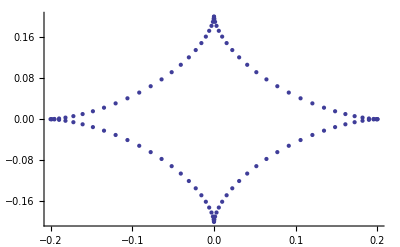
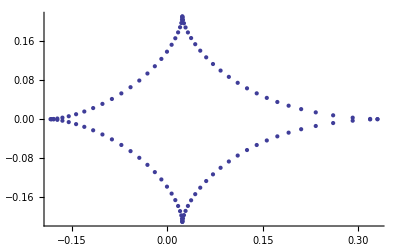
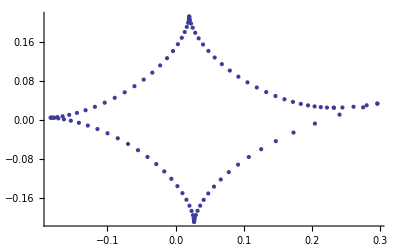
```mathematica
Show[p1,-Graphics-]
Show[p2,-Graphics-]
Show[p3,-Graphics-]
```

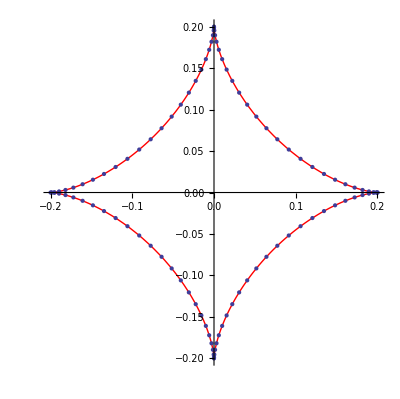

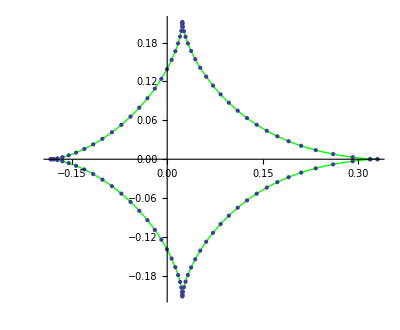

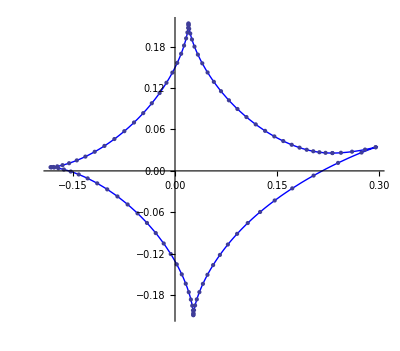

```mathematica
Lista1 =ReadList["tang_caust.dat", Number,RecordLists->True];
```

```mathematica
ListPlot[Lista1]
```

-Graphics-